```mathematica
k = 5
```

5

```mathematica
range ={-100,100}
```

{-100,100}

```mathematica
NN = RandomInteger[{10,20},k]
```

{11,17,14,10,12}

```mathematica
σ = RandomReal[{100,100}, k]
```

{100.,100.,100.,100.,100.}

```mathematica
centroids = RandomReal[range,{k,2}]
```

{{-21.7037,-92.1433},{73.7451,-59.4778},{-34.1706,22.5167},{-77.9969,-75.8477},{-55.3797,-45.0425}}

```mathematica
X =Table[
 RandomVariate[MultinormalDistribution[centroids[[i]], DiagonalMatrix[{σ[[i]],σ[[i]]}]],NN[[1]]], {i, 1, k}]
```

{{{-25.551,-86.6653},{-16.7628,-82.3717},{-16.615,-93.8563},{-24.5737,-86.2292},{-36.7103,-108.524},{-13.8818,-91.7548},{-25.6757,-100.302},{-18.819,-82.9481},{-29.7176,-99.4743},{-34.3201,-95.0187},{-12.9212,-110.588}},{{80.7388,-54.2104},{76.1516,-55.6754},{71.9099,-66.1097},{78.6485,-47.5172},{74.6009,-58.0574},{86.1247,-56.9547},{77.0164,-57.7084},{76.0602,-59.0759},{91.1537,-52.7828},{64.5746,-59.4684},{82.5731,-59.2251}},{{-29.909,26.7412},{-35.1072,31.1035},{-40.5245,8.26829},{-21.8751,28.2806},{-35.4948,24.51},{-40.7308,15.5188},{-31.5408,21.7639},{-41.8131,13.2917},{-16.3013,18.3558},{-34.9617,22.1208},{-35.2211,12.7367}},{{-61.9205,-69.4724},{-83.614,-66.0898},{-70.9061,-79.7156},{-71.4595,-63.9026},{-92.5964,-76.2251},{-75.2345,-71.387},{-75.2627,-76.4812},{-92.2577,-75.0811},{-86.1662,-80.9892},{-82.9795,-88.7461},{-73.9844,-74.6954}},{{-66.4283,-43.5489},{-49.0725,-58.905},{-48.4205,-39.5382},{-57.5157,-55.7462},{-56.7009,-51.3201},{-45.314,-54.2054},{-52.4997,-34.935},{-54.336,-52.6509},{-62.6273,-28.4045},{-54.5697,-39.333},{-60.6535,-53.7795}}}

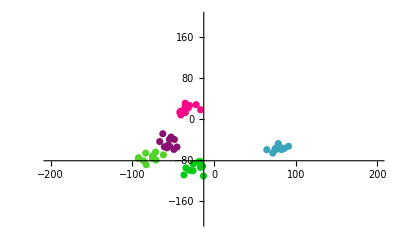

```mathematica
Show[Table[ListPlot[Style[X[[i]], RandomColor[]]],{i,1, k}], PlotRange->{2 range,2 range}]
```

```mathematica
initCentroids =  RandomReal[range,{k,2}]
```

{{-77.7338,-60.875},{-43.8685,40.6911},{95.7541,96.7867},{-89.3284,-43.4907},{0.912262,-5.83904}}

```mathematica
assignCluster[centroids_]:=((Position[#, Min[#]] //Flatten)[[1]]&  @ (Norm /@(centroids- ConstantArray[#, Length[centroids]])))& /@ Flatten[X, 1]
```

```mathematica
calCentroids[clusterassignment_] :=Table[Mean[Flatten[X, 1][[Position[clusterassignment,i]//Flatten]  ]],{i, 1, k}]//fillMissingCentroids
```

```mathematica
fillMissingCentroids[centroids_] := ReplacePart[centroids,Thread[#->RandomReal[range,{Length[#], 2}]]]& @ (Position[centroids,Mean[__]]//Flatten)
```

```mathematica
cluster[centroids_] := cluster[centroids, ConstantArray[{0,0}, Length[centroids]]]
```

```mathematica
cluster[centroids_, prevCentroids_] :=centroids /; Fold[Plus, 0, Norm /@(prevCentroids-centroids)] ≤.1
```

```mathematica
cluster[centroids_, prevCentroids_] :=cluster[calCentroids[assignCluster[centroids]], centroids]  /; Fold[Plus, 0, Norm /@(prevCentroids-centroids)] >.1
```

```mathematica
clusters =cluster[initCentroids]
```

{{-23.2317,-94.3393},{-33.0436,20.2447},{-55.2853,-46.5788},{-78.7619,-74.7987},{78.1411,-56.9805}}

```mathematica
clusterAssignment =assignCluster[clusters]
```

{1,1,1,1,1,1,1,1,1,1,1,5,5,5,5,5,5,5,5,5,5,5,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3}

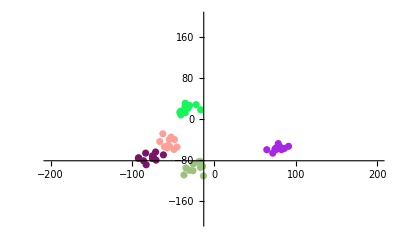

```mathematica
Show[Table[ListPlot[Style[ Flatten[X,1][[Position[clusterAssignment, i]//Flatten]], RandomColor[]]],{i,1,k}],PlotRange->{2 range,2 range}]
```